# 二维第一个子集 只显示和

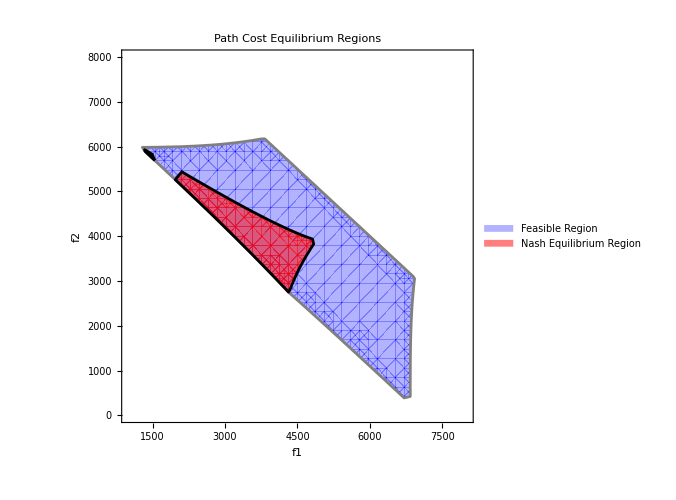

```mathematica
x1=f1;
x2=f2;
x3=10000-f1-f2;
x5=10000-f1-f2;
x8=10000-f1-f2;
e=35;
rho=15;
sigma=0.02;

link1=18*(1+0.15*(x1/3600)^4);
link2=22.5*(1+0.15*(x2/3600)^4);
link3=12*(1+0.15*(x3/1800)^4);
link5=2.4*(1+0.15*(x5/1800)^4);
link8=12*(1+0.15*(x8/1800)^4);

path1=link1+rho*(1-Exp[-sigma*link1]);
path2=link2+rho*(1-Exp[-sigma*link2]);
path5=link3+link5+link8+rho*(1-Exp[-sigma*(link3+link5+link8)]);

m1=20;
m2=15;
m5=2;

p1=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&&(path1-path2)*(m1-m2)<0&&(path1-path5)*(m1-m5)<0&&(path2-path5)*(m2-m5)<0&&10000-f1-f2>=0,{f1,1000,8000},{f2,0,8000},Axes->True,Mesh->None,BoundaryStyle->Black,PlotStyle->Directive[Red,Opacity[0.5]],FrameTicksStyle->Directive[Black,FontSize->14],FrameLabel->{Style["f1",16],Style["f2",16]},PlotLegends->{"Nash Equilibrium Region"}];

p2=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&& f1+f2<=10000,{f1,1000,8000},{f2,0,8000},Axes->True,Mesh->None,BoundaryStyle->{Thick, Gray},PlotStyle->Directive[Blue,Opacity[0.3]],FrameTicksStyle->Directive[Black,FontSize->14],FrameLabel->{Style["f1",16],Style["f2",16]},PlotLegends->{"Feasible Region"}];

Show[p2,p1,ImageSize->500,PlotLabel->Style["Path Cost Equilibrium Regions",18,Black]]
```

# 三维 第一个子集 只显示和

```mathematica
lft[t0_,x_,c_]:=t0 (1+0.15 (x/c)^4)
zeta=15;

pt1[f1_]:=lft[18,f1,3600];
pt2[f2_]:=lft[22.5,f2,3600];
pt5[f5_]:=2*lft[12,f5,1800]+lft[2.4,f5,1800];
 max[f1_,f2_,f5_] = Max[pt1[f1],pt2[f2],pt5[f5]];
 min[f1_,f2_,f5_] = Min[pt1[f1],pt2[f2],pt5[f5]];
m1 = 20;
m2 = 15;
m5 = 2;
p1=ParametricPlot3D[{u,v,10000-u-v},{u,1000,10000},{v,1000,10000},RegionFunction->Function[{u,v,f5},max[u,v,f5]-min[u,v,f5]<=zeta],PlotPoints->220,Mesh->None,AxesLabel->{"f1","f2","f5"},PlotLabel->"Feasible region on f1 + f2 + f5 = 10000",PlotStyle->Opacity[0.6,Blue]];

p2=ParametricPlot3D[{u,v,10000-u-v},{u,1000,10000},{v,1000,10000},RegionFunction->Function[{u,v,f5},max[u,v,f5]-min[u,v,f5]<zeta && pt1[u] <=pt2[v]&&pt2[v]<= pt5[f5]],PlotPoints->200,Mesh->None,AxesLabel->{"f1","f2","f5"},PlotLabel->"Feasible region on f1 + f2 + f5 = 10000",PlotStyle->Opacity[0.6,Red]];
Show[p2,p1]
```

-Graphics3D-

# 三维 第二个子集，显示 , 可接受路径集

```mathematica
ClearAll[lft,costs];
lft[c_,f_,denom_]:=c (1+0.15 (f/denom)^4);

total=10^4;
regionConstraint[{f1_,f2_,f5_},α_,ζ_]:=Module[{s=total-f1-f2-f5,f3,f4,pts},If[s<0,Return[False]];(*必须显式写 s≥0*)f3=α s;
f4=(1-α) s;
pts={lft[18,f1,3600],lft[22.5,f2,3600],lft[12,f3+f5,1800]+lft[24,f3,1800],lft[24,f4,1800]+lft[12,f4+f5,1800],lft[12,f3+f5,1800]+lft[2.4,f5,1800]+lft[12,f4+f5,1800]};
Max[pts]-Min[pts]<=ζ              (*成本波动约束*)];

Manipulate[
RegionPlot3D[
regionConstraint[{f1,f2,f5},α,ζ],
{f1,3000,6100},{f2,1200,6100},{f5,0,2200},
(*关键改动↓↓↓*)
PlotPoints->60,(*更高分辨率*)
MaxRecursion->2,(*自动再细分边界*)
WorkingPrecision->50,(*提升数值精度，避免漏采样*)
EvaluationMonitor:>Sow[{f1,f2,f5}],(*可视化采样点时调试*)
PlotStyle->Directive[Opacity[0.9],Darker[Green,0.2]],
BoundaryStyle->None,
Mesh->None,
AxesLabel->(Style[#,14,Bold]&/@{"f₁","f₂","f₅"}),
Boxed->False,Lighting->"Neutral"],
{{α,0.5,Style["α  (f₃ : f₄)",11]},0,1},
{{ζ,15,Style["ζ  (成本差上限)",11]},0,100},
ControlPlacement->Left,TrackedSymbols:>{α,ζ}
]
```

# 三维 第二个子集，显示 , 双目标可接受路径集

```mathematica
(*──────────────── 0. 公共函数与参数 ────────────────*)(*{f1,3000,6100},{f2,1200,6100},{f5,0,2200},*)
ClearAll[lft,costList];
lft[c_,f_,denom_]:=c (1+0.15 (f/denom)^4);

total=10^4;                 (*流量总量*)
αFix=0.5;                  (*f3:f4 分配比例*)
ζFix=15;                   (*成本最大波动*)

(*计算五条路径成本*)
costList[{f1_,f2_,f5_},α_]:=Module[{s,f3,f4},
s=total-f1-f2-f5;
If[s<0,Return[$Failed]];(*质量守恒不满足直接剔除*)
f3=α s;
f4=(1-α) s;
{lft[18,f1,3600],(*pt1*)
lft[22.5,f2,3600],(*pt2*)
lft[12,f3+f5,1800]+lft[24,f3,1800],(*pt3*)
lft[24,f4,1800]+lft[12,f4+f5,1800],(*pt4*)
lft[12,f3+f5,1800]+lft[2.4,f5,1800]+lft[12,f4+f5,1800]}(*pt5*)
];

(*──────────────── 1. 原始可行域 ────────────────*)
origRegionPlot=RegionPlot3D[
With[{pts=costList[{f1,f2,f5},αFix]},
If[pts===$Failed,False,Max[pts]-Min[pts]<=ζFix          (*仅成本差约束*)]
],
{f1,4000,7000},{f2,1500,6000},{f5,0,2500},
PlotPoints->60,
MaxRecursion->15,
WorkingPrecision->50,
Mesh->None,
PlotStyle->Directive[Opacity[0.25],ColorData["TemperatureMap"][#3]&],
BoundaryStyle->None];

(*──────────────── 2. 强化可行域（新增次序约束） ────────────────*)
strongRegionPlot=RegionPlot3D[
With[{pts=costList[{f1,f2,f5},αFix]},
If[pts===$Failed,False,
Max[pts]-Min[pts]<=ζFix&&(*原约束*)
pts[[3]]>pts[[5]]&&(*pt3>pt5*)
pts[[4]]>pts[[5]]&&(*pt4>pt5*)
pts[[5]]>pts[[2]]&&(*pt5>pt2*)
pts[[2]]>pts[[1]](*pt2>pt1*)]
],
{f1,3000,5000},{f2,2000,5000},{f5,0,2500},
PlotPoints->60,
MaxRecursion->15,
WorkingPrecision->50,
Mesh->None,
PlotStyle->Directive[Opacity[0.85],Darker[Red,0.1]],
BoundaryStyle->None];

(*──────────────── 3. 合并显示 ────────────────*)
Show[
origRegionPlot,(*透明青色->原可行域*)
strongRegionPlot,(*深红->强化区域*)
Boxed->False,
Axes->True,
AxesLabel->(Style[#,14,Bold]&/@{"f₁","f₂","f₅"}),
Lighting->"Neutral",
PlotRange->Automatic,
ImageSize->Large
]
```

-Graphics3D-

```mathematica
Show[%80,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Export["/Users/jinghong/Documents/Code/Python_BRUE/1.ply",%81,"PLY"]
```

/Users/jinghong/Documents/Code/Python_BRUE/1.ply

```mathematica
Rasterize[%81,"Image"]
```

```mathematica
Export["/Users/jinghong/Documents/Code/Python_BRUE/1.obj",%81,"OBJ"]
```